## ChooseTmat_all.nb (run ChooseTmat.nb first) Choose a set of elastic maps to analyze

```mathematica
TmatShow=TmatallBrown;
```

```mathematica
TmatShow=TmatallBrownAbramson;
```

```mathematica
TmatShow=TmatZenodo;
```

```mathematica
TmatShow=TmatZenodoAlphabetical;
```

#### check for missing MatrixNote

```mathematica
Map[MatrixNote,TmatShow]
Map[MatrixShortNote,TmatShow]
```

```mathematica
(* TmatTable[TmatallTRIV,2]*)
```

```mathematica
(* TmatTable[TmatallTT24,0] *)
```

```mathematica
TmatTable[TmatShow]
```

#### list the contours for each map (this can take awhile, since numerical maximization is needed)

```mathematica
Do[contoursResult=contours[TmatShow[[i]],MONO];
Print["contours for ",Tlab[TmatShow[[i]]]," (",i,"): ",contoursResult],{i,Length[TmatShow]}]
```

```mathematica
(*Column[Map[contours[#,MONO]&,TmatShow]]*)
```

```mathematica
Column[Flatten[Transpose[{
MatrixNote/@TmatShow,
"contours are "<>ToString[contours[#,MONO]]&/@TmatShow,"MaxForScalingMONO is "<>ToString[MaxForScaling[#,MONO]]&/@TmatShow,
"βISO is "<>ToString[N[βT[#,ISO]]/Degree]&/@TmatShow,
"---"&/@TmatShow}],1]]
```

#### get the rotation matrix associated with the MAX of alphaMONO

```mathematica
ntry=1000;
getUmax[Tmat_,Σ_]:=Module[{maxValue=-∞,bestRotationMatrix},
Do[Q=RandomRotation;
alpha=AlphaOfU[Tmat,Q,Σ];
If[alpha>maxValue,maxValue=alpha;
bestRotationMatrix=Q;],{ntry}];
Print["alpha-max: ",maxValue/Degree];
Print["rotation matrix: ",MatrixForm[bestRotationMatrix]];
bestRotationMatrix]
```

```mathematica
Tmat=TmatIgel;
Σ=MONO;
```

```mathematica
Umax=getUmax[Tmat,Σ];
MatrixForm[Umax]
```

#### recover alphamax using Umax

```mathematica
MatrixNote[Tmat]
TMONOmax=ProjToVSigOfU[Tmat,Umax,MONO];
AngleMatrix[Tmat,TMONOmax]/Degree
```

## Scatterplots of various quantities

#### calculate distances each map (this takes awhile, since numerical minimization is needed)

```mathematica
dTMONO=Chop[dT[#,MONO],0.001]&/@TmatShow;
```

#### remove any maps that are not TRIV, since we’ll be plotting log(dMONO) below

```mathematica
Dimensions[TmatShow]
inds=Flatten[Position[dTMONO,x_/;x>0.01]]
TmatShowSub=TmatShow[[inds]];
Dimensions[TmatShowSub]
```

#### calculate Umax for each map (this takes awhile, since numerical maximization is needed)

```mathematica
(*Umaxall=getUmax[#,MONO]&/@TmatShowSub;*)
```

#### max distance takes awhile since it involves numerical maximization

```mathematica
dTMONOmax=NormMatrix[#] Sin[AngleMatrix[#,ProjToVSigOfU[#,getUmax[#,MONO],MONO]]]&/@TmatShowSub;
```

#### distances

```mathematica
dTMONO=Chop[dT[#,MONO],0.001]&/@TmatShowSub;
dTISO=Chop[N[dT[#,ISO]],0.001]&/@TmatShowSub;
```

#### angles

```mathematica
pβTISO =N[βT[#,ISO]]/Degree&/@TmatShowSub;
pβTMONO =N[βT[#,MONO]]/Degree&/@TmatShowSub;
pMaxAlphaSubMONO =MaxAlphaSubSigma[#,MONO]&/@TmatShowSub;
pMatrixShortNote=MatrixShortNote[#]&/@TmatShowSub;
Pmin[p1_,p2_]:=Min[Flatten[{p1,p2}]];
Pmax[p1_,p2_]:=Max[Flatten[{p1,p2}]];
```

#### functions for making scatter plots

```mathematica
splot45[p1_,p2_,s1_,s2_]:=ListPlot[Transpose[{p1,p2}],PlotStyle->PointSize[0.02],
GridLines->Automatic,PlotRange->{{0,1.1Pmax[p1,p2]},{0,1.1Pmax[p1,p2]}},AspectRatio->1,Frame->True,FrameLabel->{s1,s2},Epilog->{Dashed,Red,Thickness[0.005],Line[{{0,0},Pmax[p1,p2] {1,1}}],Table[Text[Style[pMatrixShortNote[[i]],Black],{p1[[i]],p2[[i]]},{-1.75,0}],{i,Length[p1]}]},ImageSize->500,PlotLabel->Style[ToString[Length[p1]]<>" elastic maps",16],
FrameStyle->Directive[FontSize->18],FrameTicksStyle->Directive[FontSize->16]]
```

```mathematica
splot45log[p1_,p2_,s1_,s2_]:=ListLogLogPlot[Transpose[{p1,p2}],PlotStyle->PointSize[0.02],
AspectRatio->1,PlotRange->{{0.5Pmin[p1,p2],2Pmax[p1,p2]},{0.5Pmin[p1,p2],2Pmax[p1,p2]}},GridLines->Automatic,Frame->True,FrameLabel->{s1,s2},
Epilog->{Table[Text[pMatrixShortNote[[i]],Log@{p1[[i]],p2[[i]]},{-1.75,0}],{i,Length[p1]}],
Dashed,Red,Thickness[0.005],Line[{Min[Log[p1]]{1,1},Max[Log[p1]]{1,1}}]},
ImageSize->500,PlotLabel->Style[ToString[Length[p1]]<>" elastic maps",16],
FrameStyle->Directive[FontSize->18],FrameTicksStyle->Directive[FontSize->16],PlotRangeClipping->False]
```

```mathematica
splot[p1_,p2_,s1_,s2_]:=ListPlot[Transpose[{p1,p2}],PlotStyle->PointSize[0.02],
AspectRatio->1,PlotRange->Automatic,GridLines->Automatic,Frame->True,FrameLabel->{s1,s2},
Epilog->{Table[Text[pMatrixShortNote[[i]],{p1[[i]],p2[[i]]},{-1.75,0}],{i,Length[p1]}]},ImageSize->500,PlotLabel->Style[ToString[Length[p1]]<>" elastic maps",16],
FrameStyle->Directive[FontSize->18],FrameTicksStyle->Directive[FontSize->16]]
```

## Example plots

```mathematica
splot45[pβTISO,pMaxAlphaSubMONO,"βTISO","MaxAlphaSubMONO"]
```

```mathematica
splot45log[dTISO,dTMONOmax,"dTISO","dTMONOmax"]
```

```mathematica
splot45log[dTISO,dTMONO,"dTISO","dTMONO"]
```

```mathematica
splot[pβTISO,pβTMONO,"βTISO","βTMONO"]
```

```mathematica
splot[pβTISO,dTISO,"βTISO","dTISO"]
```

```mathematica
splot[pβTMONO,dTMONO,"βTMONO","dTMONO"]
```

```mathematica
splot45log[dTMONO,dTMONOmax,"dTMONO","dTMONOmax"]
```

## Angle between matrices

```mathematica
nmat=Length[TmatShow]
npair=nmat^2-nmat
```

```mathematica
Dimensions[TmatShow]
CmatShow=Map[CmatOfTmat,TmatShow];
Dimensions[CmatShow]
```

```mathematica
angleMat[m1_,m2_]:=N[MakeReal[AngleMatrix[m1,m2]]]/Degree;
(*angleMat[m1_,m2_]:=AngleMatrix[m1,m2]/Degree;*)
PT=Flatten[Outer[angleMat,TmatShow,TmatShow,1]];
PC=Flatten[Outer[angleMat,CmatShow,CmatShow,1]];
```

```mathematica
mina=0.01;
Dimensions[PT]
Dimensions[PC]
PT=Select[PT,#>=mina&];
PC=Select[PC,#>=mina&];
pmax=1.05Max[Flatten[{PT,PC}]]
Dimensions[PT]
Dimensions[PC]
```

```mathematica
sta=Style["∠",24];
stT=Style["( Ti, Tj )",16];
stC=Style["( Ci, Cj )",16];
```

```mathematica
p1=ListPlot[Transpose[{PT,PC}],PlotStyle->PointSize[0.01],GridLines->Automatic,PlotRange->{{0,pmax},{0,pmax}},AspectRatio->1,Frame->True,FrameLabel->{Row[{sta,stT}],Row[{sta,stC}]},Epilog->{Dashed,Red,Thickness[0.005],Line[{{0,0},pmax {1,1}}]},ImageSize->400,PlotLabel->Style[ToString[nmat]<>" elastic maps, "<>ToString[npair]<>" comparisons",16]];
p2=ListPlot[Transpose[{PT,PT-PC}],PlotStyle->PointSize[0.01],GridLines->Automatic,PlotRange->{{0,pmax},All},Frame->True,FrameTicks->{True,True,False,False},FrameLabel->{Row[{sta,stT}],Row[{sta,stT," - ",sta,stC}]},ImageSize->400,Epilog->{Dashed,Red,Thickness[0.005],Line[{{0,0},{pmax,0}}]}];
p3=ListPlot[Transpose[{PT,Log[PT/PC]}],PlotStyle->PointSize[0.01],GridLines->Automatic,PlotRange->{{0,pmax},All},Frame->True,FrameTicks->{True,True,False,False},FrameLabel->{Row[{sta,stT}],Style["ln[∠(Ti,Tj) / ∠(Ci,Cj)]",16]},ImageSize->400,Epilog->{Dashed,Red,Thickness[0.005],Line[{{0,0},{pmax,0}}]}];
Column[{p1,p2,p3}]
```

## Saved figures

#### Brown, Angel, Ross (2016) feldspars

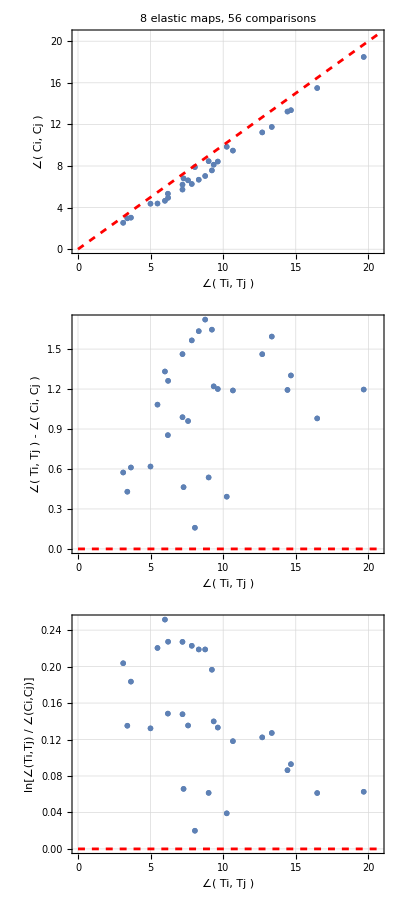

#### Brown and Abramson (2016) amphiboles

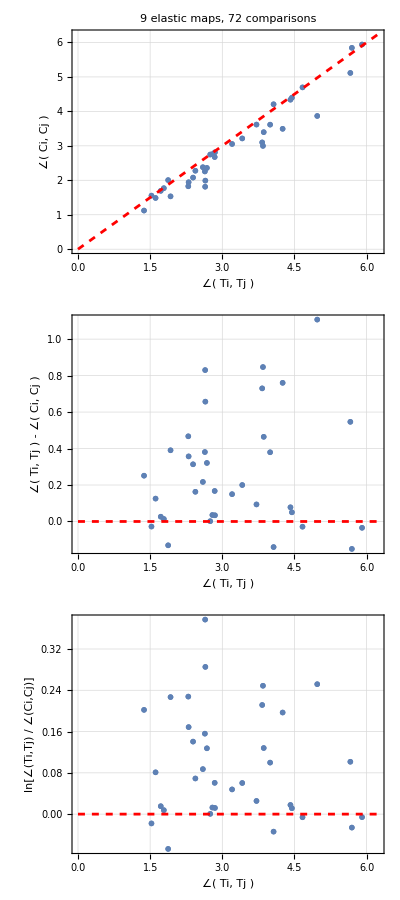

#### 28 maps in Zenodo collection (Tape and Gupta, 2024)

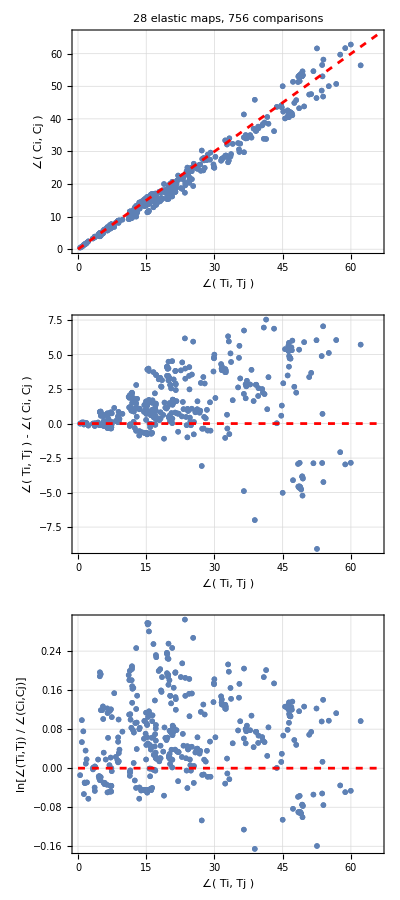

## Analytical expressions

```mathematica
Clear[a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v]
Clear[ax,bx,cx,dx,ex,fx,gx,hx,ix,jx,kx,lx,mx,nx,ox,px,qx,rx,sx,tx,ux,vx]
```

```mathematica
Tmat1=BlankSlate;
Cmat1=CmatOfTmat[Tmat1];
Tmat2=BlankSlatePrime;
Cmat2=CmatOfTmat[Tmat2];
```

```mathematica
PT=AngleMatrix[Tmat1,Tmat2];
PC=AngleMatrix[Cmat1,Cmat2];
```

#### Not very informative:

```mathematica
(*FullSimplify[PT]
FullSimplify[PC]*)
```

#### These took a LONG time and resulted in obvious expressions:

```mathematica
(* FullSimplify[PT/PC]
FullSimplify[PT-PC] *)
```